```mathematica
Задание 1. Арифметические вычисления
```

```mathematica
Пробел выполняет роль знака умножния:
```

```mathematica
3 5 (*пробел автоматически ставит умножение*)
```

15

```mathematica
Введение дополнительных пробелов не изменяют результата вычислений:
```

```mathematica
3      5
```

15

```mathematica
2+   7
```

9

```mathematica
3      /7
```

3/7

```mathematica
Целые, рациональные и иррациональные числа считаются заданными точно. Поэтому в выражениях, содержащих только такие числа, при обработке производятся лишь возможные упрощения, но сами они остаются точными и преобразуются в числа, заданные приближенно, только по команде пользователя.
```

```mathematica
17^(1/2)
```

√17

```mathematica
2/3
```

2/3

```mathematica
Действительные числа, содержащие десятичную точку, считаются заданными приближенно. Поэтому выражения, в которые входят действительные числа, вычисляются при обработке секции без специальной команды.
```

```mathematica
17.^(1/2)
```

4.12311

```mathematica
Для изменения стандартного порядка выполнения операций используются скобки
```

```mathematica
7 (1 + 2)
```

21

```mathematica
Задание 2.
```

```mathematica
N[Sqrt[17], 200]
```

4.1231056256176605498214098559740770251471992253736204343986335730949543463376215935878636508106842966845440409392141416153014208404158683630795481457469069776770232664362408630877905675723857082255214

```mathematica
Precision[%] 
(*точность вычисления*)
(*% - ссылка на предыдущий результат. %% - предпоследний и т.д.*)
```

200.

```mathematica
N[Sqrt[17]]
```

4.12311

```mathematica
Sqrt[17]
```

√17

```mathematica
var1 = N[E^(Pi*Sqrt[163]), 40]
var2 = Round[var1]
Round[3.5]
var2 - var1
```

2.625374126407687439999999999992500725972×10^17

262537412640768744

4

7.499274028×10^-13

```mathematica
(10*((10.8*10^3)/300)^(1/2)+4)^(1/3)
```

4.

```mathematica
(10^-24*10^12)/10^-14 √(32768/2^9)
```

800

```mathematica
5>3
5<2
```

True

False

```mathematica
Pi^E>E^Pi
```

False

```mathematica
N[Pi^E]
N[E^Pi]
```

22.4592

23.1407

```mathematica
Задание 3. Численное решение уравнений
-Graphics-
```

```mathematica
NSolve[√(x+2)+4*x == 4, x]
NSolve[x^3-3*x^2+5== 0, x]
```

{{x→0.597111}}

{{x→-1.1038},{x→2.0519-0.565236 ⅈ},{x→2.0519+0.565236 ⅈ}}

```mathematica
NSolve[{x^2+x*y+y^2==1, x^3+x^2*y+x*y^2+y^3==4}, {x,y}]
```

{{x→-1.-1.41421 ⅈ,y→-1.+1.41421 ⅈ},{x→-1.+1.41421 ⅈ,y→-1.-1.41421 ⅈ},{x→1.6838+0.133552 ⅈ,y→-0.683802-1.13355 ⅈ},{x→1.6838-0.133552 ⅈ,y→-0.683802+1.13355 ⅈ},{x→-0.683802-1.13355 ⅈ,y→1.6838+0.133552 ⅈ},{x→-0.683802+1.13355 ⅈ,y→1.6838-0.133552 ⅈ}}

```mathematica
NSolve[{x-y^2+3*z ==34, x+y-z==-1, -x+2*y+3*z ==4}, {x,y,z}]
```

{{x→9.25-10.2317 ⅈ,y→-3.5+4.09268 ⅈ,z→6.75-6.13901 ⅈ},{x→9.25+10.2317 ⅈ,y→-3.5-4.09268 ⅈ,z→6.75+6.13901 ⅈ}}

```mathematica
NSolve[{x^3+y^2+7*x^2*y+4*y^2*x==72,x+7*y==22}, {x,y}]
```

{{x→-223.62,y→35.0885},{x→1.065,y→2.99071},{x→-3.19541,y→3.59934}}

```mathematica
Задание 4. Вариант 4
```

```mathematica
FindRoot[x^5+x^4-2*x^3-5*x-2 == x^3, {x, -1,2}]
(*заменить -1 на 1*)
```

{x→-0.367826}

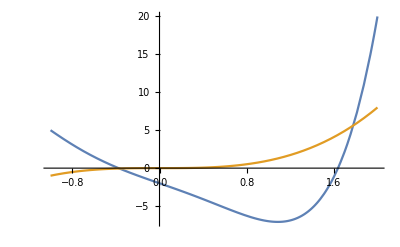

```mathematica
Plot[{x^5+x^4-2*x^3-5*x-2, x^3}, {x, -1,2}]
```

```mathematica
Задание 5. Численное решение дифференциальных уравнений
```

```mathematica
func1=NDSolve[{y''[x]+ Cos[x]*y'[x]-x^2==0, y[0]==0, y'[0]==2},y, {x,-5,2}]
```

{{y→InterpolatingFunction[…]}}

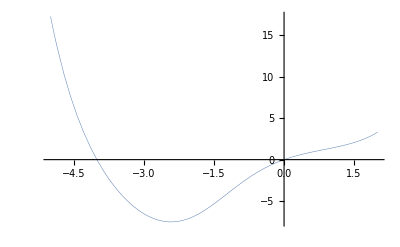

```mathematica
Plot[y[x]/.func1, {x,-5,2}, 
PlotStyle->{Thickness[0.0009]}]
```

```mathematica
func2=FindRoot[(y[x]/.func1)==0, {x,-4}]
func22=FindRoot[(y[x]/.func1)==0, {x,0}]
```

{x→-4.00784}

{x→0.}

```mathematica
D[y[x]/.func1,x]/.func2
D[y[x]/.func1,x]/.func22
```

{-10.1787}

{2.}

```mathematica
func3 = FindRoot[D[y[x]/.func1,x]==0, {x,-2.6}]
(*локальный минимум*)
```

{x→-2.41946}

```mathematica
y[x]/.func1/.func3
```

{-7.4998}

```mathematica
FindMinimum[y[x]/.func1[[1]], {x,-2.6}]
```

{-7.4998,{x→-2.41946}}

```mathematica
Задание 6. Обработка численных данных
```

```mathematica
var4=Table[{x,(7+3*x+1*x^2+2*x^3+9*x^4)(1+Random[Real,{-0.5,0.5}])},{x,-1,6,0.5}]
```

{{-1.,10.9289},{-0.5,7.48747},{0.,5.82879},{0.5,5.46299},{1.,32.369},{1.5,75.4622},{2.,189.942},{2.5,393.18},{3.,751.858},{3.5,1839.29},{4.,2182.49},{4.5,2757.46},{5.,4845.5},{5.5,8919.07},{6.,10055.1}}

```mathematica
var5=Table[{x,(6+2*x+13*Sin[x]+7*Cos[x])(1+Random[Real,{-0.5,0.5}])},{x,-1,6,0.5}]
```

{{-1.,-2.01772},{-0.5,3.15836},{0.,17.8955},{0.5,25.8671},{1.,32.4342},{1.5,27.9417},{2.,12.8809},{2.5,18.2952},{3.,9.15209},{3.5,1.57022},{4.,-0.391667},{4.5,0.862465},{5.,6.92277},{5.5,11.022},{6.,27.4979}}

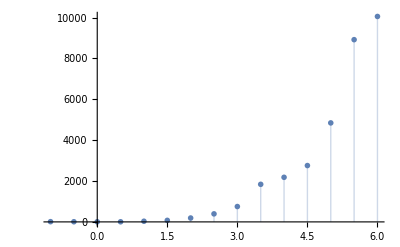

```mathematica
graph1=ListPlot[var4,PlotStyle->PointSize[0.01],Filling->Axis]
```

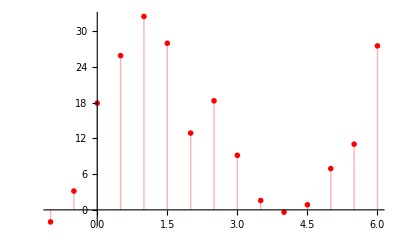

```mathematica
graph2=ListPlot[var5,PlotStyle->{PointSize[0.01], RGBColor[1,0,0]},Filling->Axis]
```

```mathematica
-Graphics-
-Graphics-
```

```mathematica
apr1=Fit[var4,{1,x,x^2,x^3,x^4,x^5,x^6},x]
```

-11.3082-582.394 x+240.696 x^2+490.529 x^3-330.736 x^4+72.8913 x^5-5.12231 x^6

```mathematica
apr2=Fit[var4,{1,x,Sin[x],Cos[x], Sin[2*x],Cos[2*x]},x]
```

-1673.69+1368.61 x+2061.2 Cos[x]+488.218 Cos[2 x]-241.514 Sin[x]-764.486 Sin[2 x]

```mathematica
apr3=Fit[var5,{1,x,Sin[x],Cos[x]},x]
```

7.61714+2.22872 x+9.17879 Cos[x]+15.7177 Sin[x]

```mathematica
apr4=Fit[var5,{1,x,x^2,x^3},x]
```

20.3616+15.3617 x-10.4351 x^2+1.34368 x^3

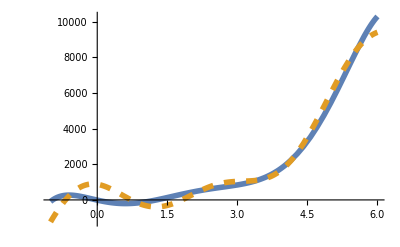

```mathematica
y1=Plot[{apr1,apr2},{x,-1,6},
PlotStyle->{{Thickness[0.01]},{Thickness[0.01],Dashing[{0.02}]}}]
```

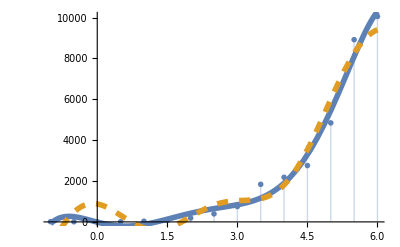

```mathematica
Show[graph1,y1]
```

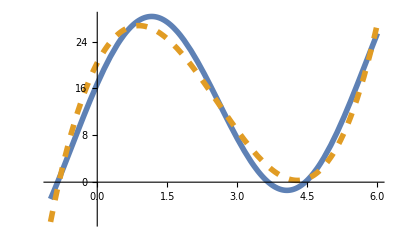

```mathematica
y2=Plot[{apr3,apr4},{x,-1,6},
PlotStyle->{{Thickness[0.01]},{Thickness[0.01],Dashing[{0.02}]}}]
```

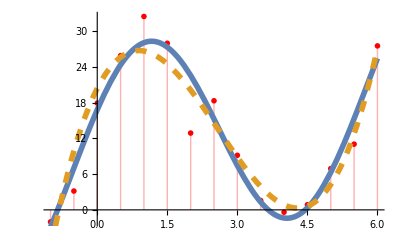

```mathematica
Show[graph2,y2]
```